L = 4

nParticles = 4

J Matrix:

(0 | J01 | J02 | J03 | J04
J01 | 0 | J12 | J13 | J14
J02 | J12 | 0 | J23 | J24
J03 | J13 | J23 | 0 | J34
J04 | J14 | J24 | J34 | 0)

Total configurations: 24

First few: {{1,2,3,4},{1,2,4,3},{1,3,2,4},{1,3,4,2},{1,4,2,3}}

Transition matrix row sums: {1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

Transition matrix:

Showing 5x5 block:

(1/2 (2-(Piecewise[{{1, J14+J23≤J13+J24}, {ⅇ^((J13-J14-J23+J24) β), J14+J23>J13+J24}, {0, True}}])-(Piecewise[{{1, J12+J34≤J13+J24}, {ⅇ^(-((J12-J13-J24+J34) β)), J12+J34>J13+J24}, {0, True}}])) | 1/4 (Piecewise[{{1, J14+J23≤J13+J24}, {ⅇ^((J13-J14-J23+J24) β), J14+J23>J13+J24}, {0, True}}]) | 1/4 (Piecewise[{{1, J12+J34≤J13+J24}, {ⅇ^(-((J12-J13-J24+J34) β)), J12+J34>J13+J24}, {0, True}}]) | 0 | 0
1/4 (Piecewise[{{1, J13+J24≤J14+J23}, {ⅇ^(-((J13-J14-J23+J24) β)), J13+J24>J14+J23}, {0, True}}]) | 1/2 (2-(Piecewise[{{1, J13+J24≤J14+J23}, {ⅇ^(-((J13-J14-J23+J24) β)), J13+J24>J14+J23}, {0, True}}])-(Piecewise[{{1, J12+J34≤J14+J23}, {ⅇ^(-((J12-J14-J23+J34) β)), J12+J34>J14+J23}, {0, True}}])) | 0 | 0 | 1/4 (Piecewise[{{1, J12+J34≤J14+J23}, {ⅇ^(-((J12-J14-J23+J34) β)), J12+J34>J14+J23}, {0, True}}])
1/4 (Piecewise[{{1, J13+J24≤J12+J34}, {ⅇ^((J12-J13-J24+J34) β), J13+J24>J12+J34}, {0, True}}]) | 0 | 1/2 (2-(Piecewise[{{1, J14+J23≤J12+J34}, {ⅇ^((J12-J14-J23+J34) β), J14+J23>J12+J34}, {0, True}}])-(Piecewise[{{1, J13+J24≤J12+J34}, {ⅇ^((J12-J13-J24+J34) β), J13+J24>J12+J34}, {0, True}}])) | 1/4 (Piecewise[{{1, J14+J23≤J12+J34}, {ⅇ^((J12-J14-J23+J34) β), J14+J23>J12+J34}, {0, True}}]) | 0
0 | 0 | 1/4 (Piecewise[{{1, J12+J34≤J14+J23}, {ⅇ^(-((J12-J14-J23+J34) β)), J12+J34>J14+J23}, {0, True}}]) | 1/2 (2-(Piecewise[{{1, J13+J24≤J14+J23}, {ⅇ^(-((J13-J14-J23+J24) β)), J13+J24>J14+J23}, {0, True}}])-(Piecewise[{{1, J12+J34≤J14+J23}, {ⅇ^(-((J12-J14-J23+J34) β)), J12+J34>J14+J23}, {0, True}}])) | 0
0 | 1/4 (Piecewise[{{1, J14+J23≤J12+J34}, {ⅇ^((J12-J14-J23+J34) β), J14+J23>J12+J34}, {0, True}}]) | 0 | 0 | 1/2 (2-(Piecewise[{{1, J14+J23≤J12+J34}, {ⅇ^((J12-J14-J23+J34) β), J14+J23>J12+J34}, {0, True}}])-(Piecewise[{{1, J13+J24≤J12+J34}, {ⅇ^((J12-J13-J24+J34) β), J13+J24>J12+J34}, {0, True}}])))

Detailed balance: SATISFIED

Decision tree for first state:

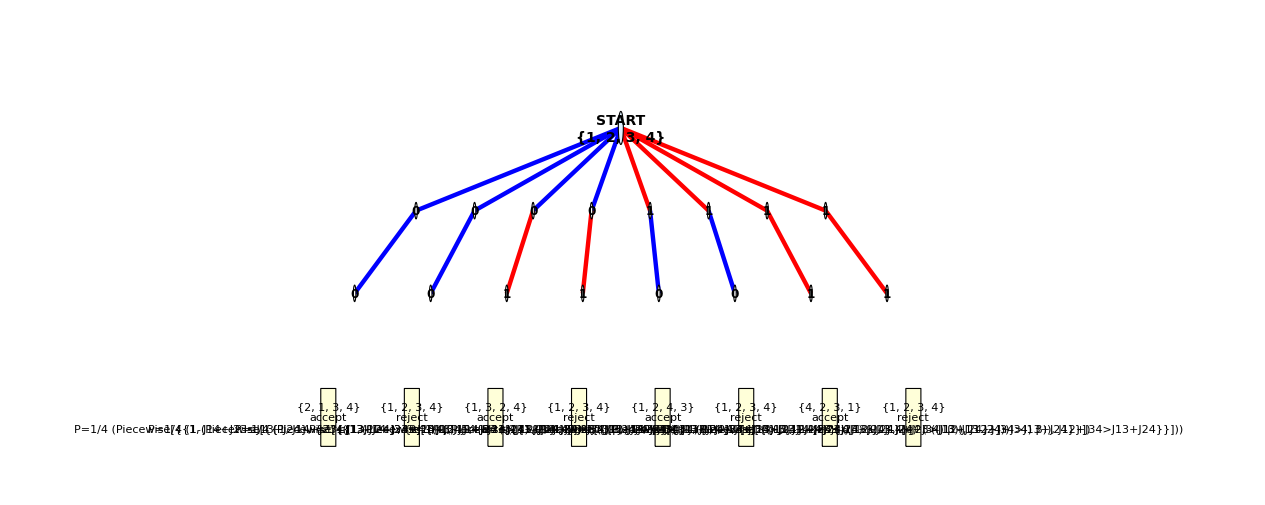

Decision tree for second state:

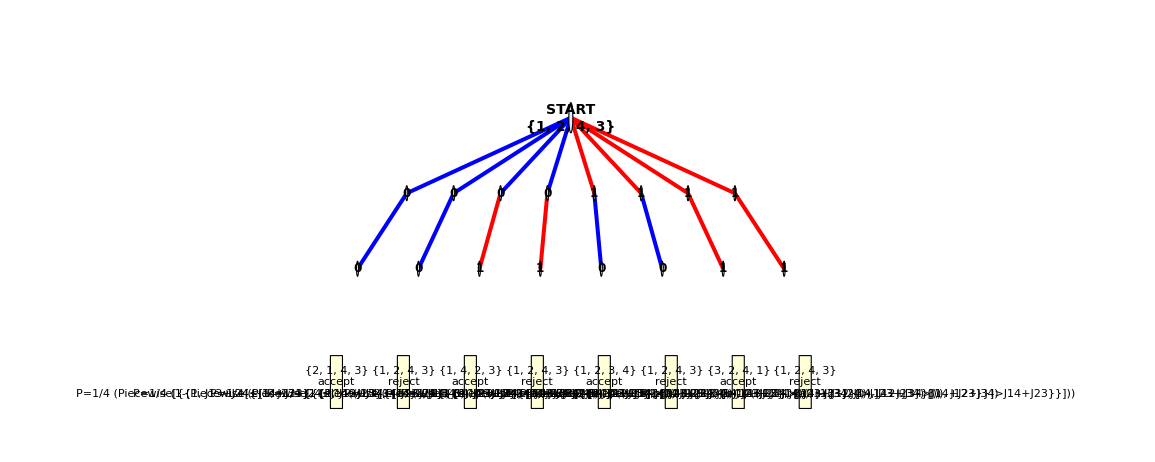

```mathematica
ClearAll["Global`*"]

(* =========================================*)
(*SETUP*)
(* =========================================*)

L=4;
nParticles=4;
β=Symbol["β"];

Print["L = ",L];
Print["nParticles = ",nParticles];

(* =========================================*)
(*SYMBOLIC J MATRIX*)
(* =========================================*)

GenerateSymbolicJ[n_]:=Module[{J=Table[0,{n+1},{n+1}]},Do[If[i<j,J[[i+1,j+1]]=Symbol["J"<>ToString[i]<>ToString[j]];
J[[j+1,i+1]]=J[[i+1,j+1]]],{i,0,n},{j,0,n}];
J]

JMatrix=GenerateSymbolicJ[nParticles];

Print["J Matrix:"];
Print[JMatrix//MatrixForm];

(* =========================================*)
(*ENERGY*)
(* =========================================*)

SymbolicEnergy[lattice_]:=Module[{E=0,i,j},Do[j=If[i==Length[lattice],1,i+1];
If[lattice[[i]]!=0&&lattice[[j]]!=0,E-=JMatrix[[lattice[[i]]+1,lattice[[j]]+1]]],{i,Length[lattice]}];
E]

(* =========================================*)
(*CONFIGURATIONS*)
(* =========================================*)

GenerateAllConfigs[L_,n_]:=Flatten[Table[Module[{lat=ConstantArray[0,L]},Do[lat[[pos[[i]]]]=perm[[i]],{i,n}];
lat],{pos,Subsets[Range[L],{n}]},{perm,Permutations[Range[n]]}],1]

states=GenerateAllConfigs[L,nParticles];
Print["Total configurations: ",Length[states]];
Print["First few: ",Take[states,Min[5,Length[states]]]];

(* =========================================*)
(*TREE RANDOMNESS*)
(* =========================================*)

$BinaryChoices={};
$BinaryIndex=1;

BinaryBit[]:=Module[{b},b=$BinaryChoices[[$BinaryIndex]];
$BinaryIndex++;
b]

DecodeInteger[nBits_]:=FromDigits[Table[BinaryBit[],{nBits}],2]

(* =========================================*)
(*KAWASAKI MOVE—normalized probabilities*)
(* =========================================*)

KawasakiMoveFromBits[lattice_]:=Module[{Lsize,nBits,raw,i,j,new,ΔE,p,siteProb},Lsize=Length[lattice];
siteProb=1/Lsize;
nBits=Ceiling[Log2[Lsize]];
raw=DecodeInteger[nBits];
i=1+Mod[raw,Lsize];
j=If[i==Lsize,1,i+1];
If[lattice[[i]]==lattice[[j]],Return[{"no-swap",lattice,siteProb}]];
new=lattice;
new[[{i,j}]]=lattice[[{j,i}]];
ΔE=SymbolicEnergy[new]-SymbolicEnergy[lattice];
p=Piecewise[{{1,ΔE<=0},{Exp[-β ΔE],ΔE>0}}];
{{"accept",new,siteProb*p},{"reject",lattice,siteProb*(1-p)}}]

(* =========================================*)
(*TREE ENUMERATION*)
(* =========================================*)

EnumerateTree[lattice_]:=Module[{nBitsForSite,allBits,results},nBitsForSite=Ceiling[Log2[Length[lattice]]];
allBits=Tuples[{0,1},nBitsForSite];
results=Flatten[Table[($BinaryChoices=bits;
$BinaryIndex=1;
With[{out=KawasakiMoveFromBits[lattice]},If[First[out]==="no-swap",{{bits,"no-swap",out[[2]],out[[3]]}},{{bits,"accept",out[[1,2]],out[[1,3]]},{bits,"reject",out[[2,2]],out[[2,3]]}}]]),{bits,allBits}],1];
results]

(* =========================================*)
(*TREE VISUALIZATION—BIG,SCROLLABLE*)
(* =========================================*)

VisualizeDecisionTree[initialState_]:=Module[{tree,nBitsForSite,nBitsTotal,yLevels,xSpacing,nodeRadius,rootX,rootY,pathGraphics,baseXPositions,imageWidth,plotRangeX,Lsize,rootGraphics},tree=EnumerateTree[initialState];
Lsize=Length[initialState];
nBitsForSite=Ceiling[Log2[Lsize]];
nBitsTotal=nBitsForSite;
(*Use a wide layout for scrolling*)imageWidth=Max[1800,Length[tree]*60];
plotRangeX=Max[50,Length[tree]*3];
yLevels=Range[nBitsTotal,0,-1]*2;
xSpacing=Max[20,Length[tree]*1.5];
nodeRadius=0.2;
rootX=0;
rootY=yLevels[[1]];
baseXPositions=Table[(i-(Length[tree]+1)/2)*(xSpacing/1.5),{i,Length[tree]}];
pathGraphics=Table[Module[{path,pathType,finalState,probability,currentX,currentY,lineGraphics,circleGraphics,labelGraphics,bit,level,nextX,nextY,edgeColor,leafY,leafX,leafColor,leafText,treeEntry},treeEntry=tree[[i]];
path=Part[treeEntry,1];
pathType=Part[treeEntry,2];
finalState=Part[treeEntry,3];
probability=Part[treeEntry,4];
currentX=rootX;
currentY=rootY;
lineGraphics={};
circleGraphics={};
labelGraphics={};
Do[bit=path[[level]];
nextX=baseXPositions[[i]]+(currentX-baseXPositions[[i]])*0.3;
nextY=yLevels[[level+1]];
edgeColor=Which[bit==0,Blue,bit==1,Red,True,Black];
AppendTo[lineGraphics,{edgeColor,Thickness[0.0025],Arrowheads[0],Arrow[{{currentX,currentY},{nextX,nextY}}]}];
AppendTo[circleGraphics,{White,EdgeForm[{Black,Thin}],Disk[{nextX,nextY},nodeRadius]}];
AppendTo[labelGraphics,Text[Style[bit,Bold,12],{nextX,nextY}]];
currentX=nextX;
currentY=nextY;,{level,Length[path]}];
leafY=-3;
leafX=baseXPositions[[i]];
{leafColor,leafText}=Which[pathType=="no-swap",{LightGray,Column[{Style[ToString[finalState],Gray,12],Style["no-swap",Gray,10]},Center,Spacings->0.1]},pathType=="accept",{LightYellow,Column[{Style[ToString[finalState],Black,Bold,12],Style["accept",Black,10],Style["P="<>ToString[TraditionalForm[Simplify[probability]]],Black,10]},Center,Spacings->0.1]},pathType=="reject",{LightYellow,Column[{Style[ToString[finalState],Black,Bold,12],Style["reject",Black,10],Style["P="<>ToString[TraditionalForm[Simplify[probability]]],Black,10]},Center,Spacings->0.1]}];
AppendTo[circleGraphics,{leafColor,EdgeForm[{Black,Thin}],Rectangle[{leafX-1.2,leafY-0.7},{leafX+1.2,leafY+0.7}]}];
AppendTo[labelGraphics,Text[leafText,{leafX,leafY}]];
{lineGraphics,circleGraphics,labelGraphics}],{i,Length[tree]}];
rootGraphics={{LightBlue,EdgeForm[{Black,Thick}],Disk[{rootX,rootY},nodeRadius*2]},Text[Style["START\n"<>ToString[initialState],Bold,14],{rootX,rootY}]};
(*Wrap the tree in a scrollable pane*)Pane[Graphics[{pathGraphics,rootGraphics},PlotRange->{{-plotRangeX,plotRangeX},{-4,yLevels[[1]]+2}},AspectRatio->0.4,Background->White],{1800,600},Scrollbars->True]]

(* =========================================*)
(*TRANSITION MATRIX*)
(* =========================================*)

EnumerateTransitions[lattice_]:=Module[{tree},tree=EnumerateTree[lattice];
Merge[Table[{lattice,tree[[i,3]]}->tree[[i,4]],{i,Length[tree]}],Total]]

BuildTransitionMatrix[states_]:=Module[{n,idx,M,trans},n=Length[states];
idx=AssociationThread[states->Range[n]];
M=ConstantArray[0,{n,n}];
Do[trans=EnumerateTransitions[s];
KeyValueMap[(M[[idx[#1[[1]]],idx[#1[[2]]]]]=Simplify[#2])&,trans],{s,states}];
M]

transitionMatrix=BuildTransitionMatrix[states];

Print["\nTransition matrix row sums: ",Simplify[Total[transitionMatrix,{2}]]];
Print["Transition matrix:"];
If[Length[states]<=10,Print[transitionMatrix//MatrixForm],Print["Showing 5x5 block:"];
Print[Take[transitionMatrix,{1,5},{1,5}]//MatrixForm]];

(* =========================================*)(*DETAILED BALANCE CHECK—fixed FullSimplify logic*)(* =========================================*)theoreticalDist=Table[Exp[-β*SymbolicEnergy[states[[i]]]],{i,Length[states]}];
Z=Total[theoreticalDist];
theoreticalDist=theoreticalDist/Z;

violations=Flatten[Table[theoreticalDist[[i]]*transitionMatrix[[i,j]]-theoreticalDist[[j]]*transitionMatrix[[j,i]],{i,Length[states]},{j,i+1,Length[states]}]];

(*Remove literal zeros*)
nonZero=DeleteCases[violations,0];

(*Attempt simplification if necessary*)
If[Length[nonZero]>0,Module[{fsTest},fsTest=Quiet[Check[FullSimplify[nonZero[[1]]],"FAIL"]];
(*Use PossibleZeroQ instead of===0*)If[fsTest=!="FAIL"&&PossibleZeroQ[fsTest],(*FullSimplify all violations in parallel*)nonZero=ParallelMap[FullSimplify,nonZero];]]];

Print["\nDetailed balance: ",If[Length[Select[nonZero,!PossibleZeroQ[#]&]]==0,"SATISFIED",ToString[Length[Select[nonZero,!PossibleZeroQ[#]&]]]<>" violations"]];


(* =========================================*)
(*VISUALIZE TREES FOR FIRST TWO STATES*)
(* =========================================*)

Print["\nDecision tree for first state:"];
tree1=VisualizeDecisionTree[states[[1]]];
Print[tree1];

If[Length[states]>1,Print["\nDecision tree for second state:"];
tree2=VisualizeDecisionTree[states[[2]]];
Print[tree2];];
```